## This is a guide to using the NDSolve function in Mathematica

This function can be tricky to use and understand the outputs that Mathematica is providing.

First, Using the NDSolve function returns what is known as a rule in Mathematica.

```mathematica
s=NDSolve[{f''[t]+Sin[f[t]]==0,f[0]==Pi/8,f'[0]==0},f,{t,0,10}]
```

{{f→InterpolatingFunction[…]}}

To convert a rule to a function, you do this bit of magic that I do not understand:

```mathematica
ph=f/.First[s]
```

InterpolatingFunction[…]

Now I have a function that I can evaluate and understand in the normal way.

```mathematica
ph[1]
```

0.215837

I can plot this function just like any other.

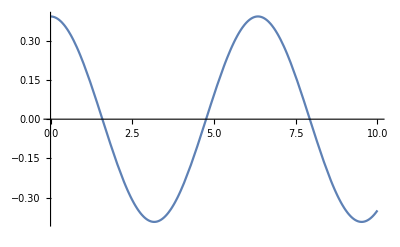

```mathematica
Plot[ph[t],{t,0,10}]
```

And parametric plots are particularly helpful for this example type of differential equations (pendulum).

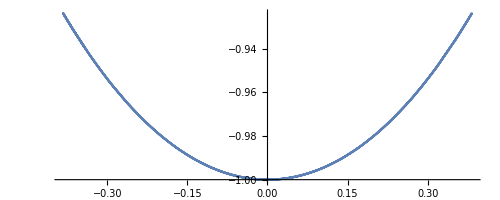

```mathematica
ParametricPlot[{Sin[ph[t]],-Cos[ph[t]]},{t,0,10}]
```

```mathematica
r = NDSolve[{(9.8+x[t])f''[t]+2x'[t]f'[t]+9.8Sin[f[t]]==0,x''[t]==(9.8+x[t])*(f'[t])^2+9.8Cos[f[t]]-10x[t],f[0]==Pi/4,x[0]==0,f'[0]==0,x'[0]==0},{f,x},{t,0,10}]
```

{{f→InterpolatingFunction[…],x→InterpolatingFunction[…]}}

```mathematica
ph1=f/.First[r]
```

InterpolatingFunction[…]

```mathematica
x1=x/.First[r]
```

InterpolatingFunction[…]

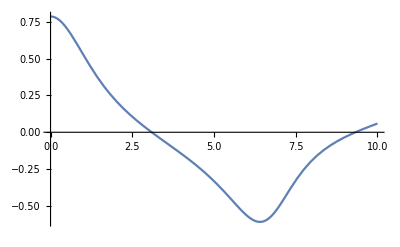

```mathematica
Plot[ph1[t],{t,0,10}]
```

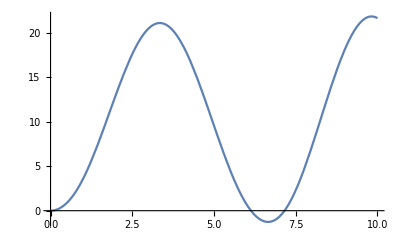

```mathematica
Plot[x1[t],{t,0,10}]
```

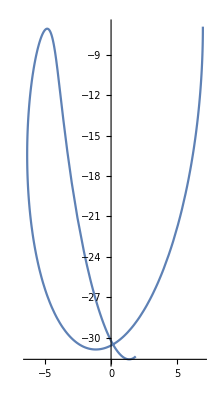

```mathematica
ParametricPlot[{(9.8+x1[t])Sin[ph1[t]],-(9.8+x1[t])*Cos[ph1[t]]},{t,0,10}]
```

```mathematica
2+2
```

```mathematica
4 √2
```

4 √2

```mathematica
N[%]
```

5.65685

```mathematica
π/(2 12^(1/3))
```

π/(2 2^(2/3) 3^(1/3))

```mathematica
y[t_]:=t^3^(2+t)
```

```mathematica
y[0]
```

0

```mathematica
y[1]
```

1

```mathematica
y[2]
```

2417851639229258349412352

```mathematica
Plot[y[t],{t,0,2},PlotRange-> All]
```

-Graphics-

```mathematica
y'[t]
```

t^(3^(2+t)) (3^(2+t)/t+3^(2+t) Log[3] Log[t])

```mathematica
N[∫_0^2 y[t]ⅆt]
```

2.39803×10^22

```mathematica
∫y[t]ⅆt
```

∫t^(3^(2+t))ⅆt

```mathematica
N[Integrate[y[t],{t,0,1}]]
```

0.0387685

```mathematica
∫
```